```mathematica
board=SparseArray[{15,15}->1,{30,30}];
dna=RandomInteger[1,512];
```

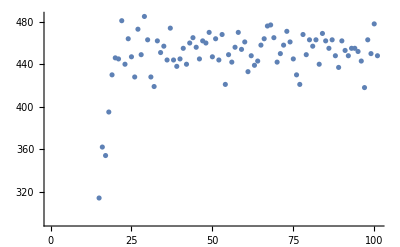

```mathematica
trace=evolveTrace[dna,100][board];ListPlot[mass/@evolveTrace[dna,100][board]]
visulaiseTrace[trace]
```